```mathematica
<<RLBot`
```

```mathematica
SetDirectory[NotebookDirectory[]];
```

```mathematica
datafiles = FileNames["*.ndjson",NotebookDirectory[]];
```

```mathematica
data = ImportNDJSON["aerial_ground_1.ndjson", {2}];
```

```mathematica
Δt = 1.0 / 120.0;
cars = #["car"] & /@ data;
inputs = #["inputs"] & /@ data;
times = #["time"] & /@ data;
actualTimes = #["actual_time"] & /@ data;
```

```mathematica
Normalize[cars[[1]]["v"]]
```

{-0.542535,0.840033,0.0000484864}

```mathematica
cars[[1]]["o"][[All, 1]]
```

{-0.541357,0.840739,-0.00949136}

```mathematica
cars[[1]]
```

<|boost_left→100,dodge_dir→{0.,5.88545×10^-44},dodge_timer→-1.,double_jumped→False,jump_timer→-1.,jumped→False,o→{{-0.541357,-0.840778,-0.00505784},{0.840739,-0.54138,0.00803203},{-0.00949136,0.0000958695,0.999955}},on_ground→True,supersonic→False,time→63.4118,v→{-570.661,883.581,0.051},w→{0.,-0.00051,0.04121},x→{2514.73,-4428.19,17.02}|>

```mathematica
times = #["time"] & /@ data;
```

```mathematica
RotationMatrix[ϕ]
```

{{Cos[ϕ],-Sin[ϕ]},{Sin[ϕ],Cos[ϕ]}}

```mathematica
Quiet[EulerAngleRotation[{p, y, r}]] // MatrixForm
```

(Cos[p] Cos[y] | Cos[y] Sin[p] Sin[r]-Cos[r] Sin[y] | -Cos[r] Cos[y] Sin[p]-Sin[r] Sin[y]
Cos[p] Sin[y] | Cos[r] Cos[y]+Sin[p] Sin[r] Sin[y] | Cos[y] Sin[r]-Cos[r] Sin[p] Sin[y]
Sin[p] | -Cos[p] Sin[r] | Cos[p] Cos[r])

```mathematica
FullSimplify[#[[1]].#[[2]].#[[3]] - Quiet[EulerAngleRotation[{-p, y,-r}]]]  & /@ Permutations[{Rx, Ry, Rz}]
```

{{{0,-Cos[y] Sin[p] Sin[r]+(-Cos[p]+Cos[r]) Sin[y],Sin[p]-Cos[r] Cos[y] Sin[p]-Sin[r] Sin[y]},{Cos[y] Sin[p] Sin[r]+(-Cos[p]+Cos[r]) Sin[y],-2 Sin[p] Sin[r] Sin[y],(-Cos[p]+Cos[y]) Sin[r]-Cos[r] Sin[p] Sin[y]},{Sin[p]-Cos[r] Cos[y] Sin[p]+Sin[r] Sin[y],(-Cos[p]+Cos[y]) Sin[r]+Cos[r] Sin[p] Sin[y],0}},{{0,-Cos[y] Sin[p] Sin[r]+(-1+Cos[r]) Sin[y],-(-1+Cos[r]) Cos[y] Sin[p]-Sin[r] Sin[y]},{Sin[p] Sin[r]+Cos[p] (-1+Cos[r]) Sin[y],-Sin[p] Sin[r] Sin[y],(-Cos[p]+Cos[y]) Sin[r]},{Sin[p]-Cos[r] Sin[p]+Cos[p] Sin[r] Sin[y],(-Cos[p]+Cos[y]) Sin[r],Sin[p] Sin[r] Sin[y]}},{{Sin[p] Sin[r] Sin[y],(-Cos[p]+Cos[r]) Sin[y],-Cos[r] (-1+Cos[y]) Sin[p]-Sin[r] Sin[y]},{(-Cos[p]+Cos[r]) Sin[y],-Sin[p] Sin[r] Sin[y],(-1+Cos[y]) Sin[r]-Cos[r] Sin[p] Sin[y]},{Sin[p]-Cos[y] Sin[p]+Cos[p] Sin[r] Sin[y],Cos[p] (-1+Cos[y]) Sin[r]+Sin[p] Sin[y],0}},{{0,-(-1+Cos[y]) Sin[p] Sin[r]-(-1+Cos[p]) Cos[r] Sin[y],-Cos[r] (-1+Cos[y]) Sin[p]+(-1+Cos[p]) Sin[r] Sin[y]},{-(-1+Cos[p]) Sin[y],-Sin[p] Sin[r] Sin[y],-Cos[r] Sin[p] Sin[y]},{-(-1+Cos[y]) Sin[p],Cos[r] Sin[p] Sin[y],-Sin[p] Sin[r] Sin[y]}},{{-Sin[p] Sin[r] Sin[y],-Cos[y] Sin[p] Sin[r],-(-1+Cos[r]) Cos[y] Sin[p]+(-1+Cos[p]) Sin[r] Sin[y]},{Cos[y] Sin[p] Sin[r],-Sin[p] Sin[r] Sin[y],-(-1+Cos[p]) Cos[y] Sin[r]-(-1+Cos[r]) Sin[p] Sin[y]},{-(-1+Cos[r]) Sin[p],-(-1+Cos[p]) Sin[r],0}},{{0,0,0},{0,0,0},{0,0,0}}}

```mathematica
Rz.Ry.Rx - Quiet[EulerAngleRotation[{p, y,r}]]  // MatrixForm
```

(0 | 0 | 0
0 | 0 | 0
0 | 0 | 0)

```mathematica
Rx = RotationMatrix[-r, {1, 0, 0}]; Rx // MatrixForm
```

(1 | 0 | 0
0 | Cos[r] | Sin[r]
0 | -Sin[r] | Cos[r])

```mathematica
Ry = RotationMatrix[-p, {0, 1, 0}]; Ry // MatrixForm
```

(Cos[p] | 0 | -Sin[p]
0 | 1 | 0
Sin[p] | 0 | Cos[p])

```mathematica
Rz = RotationMatrix[y, {0, 0, 1}]; Rx // MatrixForm
```

(1 | 0 | 0
0 | Cos[r] | Sin[r]
0 | -Sin[r] | Cos[r])

```mathematica
Rz.Ry.Rx // MatrixForm
```

(Cos[p] Cos[y] | Cos[y] Sin[p] Sin[r]-Cos[r] Sin[y] | -Cos[r] Cos[y] Sin[p]-Sin[r] Sin[y]
Cos[p] Sin[y] | Cos[r] Cos[y]+Sin[p] Sin[r] Sin[y] | Cos[y] Sin[r]-Cos[r] Sin[p] Sin[y]
Sin[p] | -Cos[p] Sin[r] | Cos[p] Cos[r])

```mathematica
Quiet[EulerAngleRotation[{p, y,r}]] // MatrixForm
```

(Cos[p] Cos[y] | Cos[y] Sin[p] Sin[r]-Cos[r] Sin[y] | -Cos[r] Cos[y] Sin[p]-Sin[r] Sin[y]
Cos[p] Sin[y] | Cos[r] Cos[y]+Sin[p] Sin[r] Sin[y] | Cos[y] Sin[r]-Cos[r] Sin[p] Sin[y]
Sin[p] | -Cos[p] Sin[r] | Cos[p] Cos[r])

```mathematica
Max[Differences[times]]
```

0.0103836

```mathematica
Max[Differences[actualTimes]]
```

0.0099744

```mathematica
Compare[fn_, actual_, predicted_] := {
fn /@ actual[[1;;Length[predicted]]],
 fn /@ predicted[[1;;Length[predicted]]]
}
```

```mathematica
count =1;
predicted = cars[[1]];
predicted["input"] = inputs[[1]];
predicted["state"] = CarStateOnGround;
predicted["dodge_torque"] ={0, 0, 0};
predictions = {predicted};
Do[
predicted = CarStep[predicted, i];
AppendTo[predictions, predicted]
,
 {i, inputs[[1;;-2]]}
]
```

```mathematica
#["state"] & /@ predictions
```

{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,1,1,1,1,1,1,1,1,1,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,3,4,4,275,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4}
 |  |  |  |

```mathematica
{xA,xP}=Compare[#["x"]&, cars, predictions];
{vA,vP}=Compare[#["v"]&, cars, predictions];
{wA,wP}=Compare[#["w"]&, cars, predictions];
{oA,oP}=Compare[#["o"]&, cars, predictions];
```

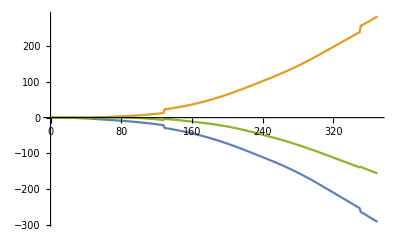

```mathematica
Show[
ListLinePlot[Transpose[xA-xP]]
]
```

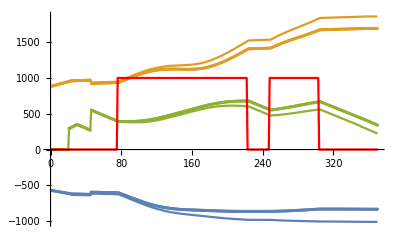

```mathematica
Show[
ListLinePlot[Transpose[vA]],
ListPlot[Transpose[vP]],
ListLinePlot[1000 (Boole[#["boost"]]& /@ inputs), PlotStyle->Red]
]
```

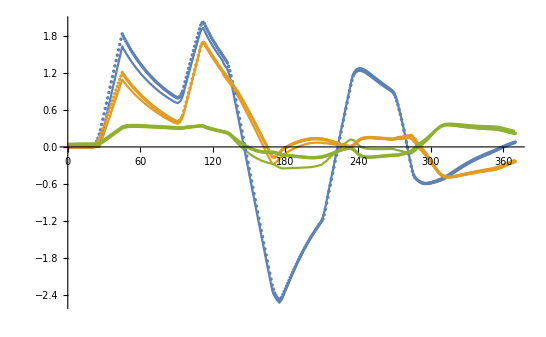

```mathematica
Show[
ListLinePlot[Transpose[wA],PlotRange->All],
ListPlot[Transpose[wP],PlotRange->All],
PlotRange->All
]
```

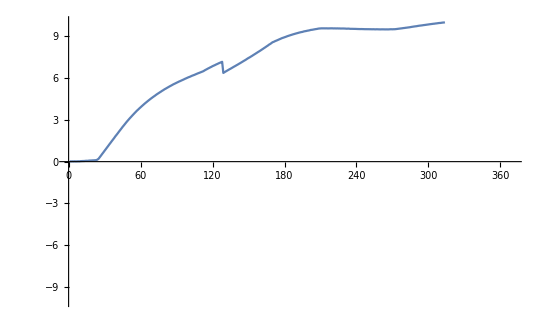

```mathematica
ListLinePlot[180/π Table[AngleBetween[oA[[i]],oP[[i]]], {i, 1, Length[oA]}], PlotRange->{-10, 10}]
```

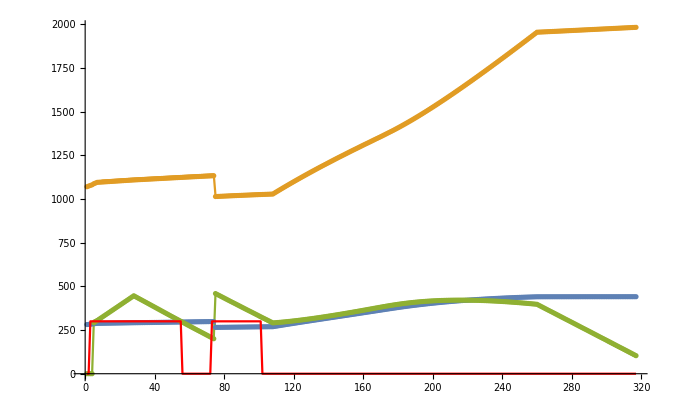

```mathematica
Show[
ListLinePlot[Transpose[vA]],
ListPlot[Transpose[vP]],
ListLinePlot[300Boole[#["jump"]]& /@ inputs, PlotStyle->Red]
]
```